## Homework 4

#### Logan Houchens and Valerie Richmond CPS371 2/28/14

1.

i.

```mathematica
findProb[]:= Module[{numDice=2, possList={},probList={0,0,0,0,0,0,0,0,0,0,0}, i, die1,die2, sum=0, finalList={}},

(*The nested loopsmake a list of all of the possible sums of two dice possibilities.*)

For[ die1=1, die1 ≤ 6, die1++, For[die2=1, die2≤ 6, die2++, AppendTo[possList, die1+die2]
]
]; 

(*The loop goes through the possible sums and records the frequency of each in another list.*)

For[i=1, i≤ Length[possList], i++, sum=possList[[i]]; probList[[sum-1]] = probList[[sum-1]]+1];

(*The loop goes through the previously created probList and creates another list with the probability.*)

For[i=1, i≤ Length[probList], i++, AppendTo[finalList,probList[[i]]/Total[probList]]];

(*The list of probabilities is returned*)
Return[finalList]
]
```

```mathematica
probabilities= findProb[];
```

```mathematica
Grid[{Range[2,12],Table[probabilities[[x]],{x,11}]},Frame->All]
```

2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
1/36 | 1/18 | 1/12 | 1/9 | 5/36 | 1/6 | 5/36 | 1/9 | 1/12 | 1/18 | 1/36

ii.

```mathematica
uDiceGame[utaPick_, clausPick_]:=Module[{utaNum= utaPick, clausNum=clausPick, utaRollSum,clausRollSum, winner=False, roll=1}, 

(*While there is no winner, Claus and Uta both roll two dice continually. If at any point one of their roll sums equals theri picked number then they win the game and the information is returned in a list.*)

While[!winner,

utaRollSum=RandomChoice[{1,2,3,4,5,6}]+RandomChoice[{1,2,3,4,5,6}];
clausRollSum=RandomChoice[{1,2,3,4,5,6}]+RandomChoice[{1,2,3,4,5,6}];

If[utaRollSum==utaNum, winner=True; Return[{utaRollSum, clausRollSum, roll}],
If[clausRollSum==clausNum, winner=True; Return[{utaRollSum, clausRollSum, roll}]]
];

roll++
]
]
```

```mathematica
uDiceGame[5,10]
uDiceGame[12,12]
uDiceGame[2,7]
```

{7,10,1}

{6,12,16}

{2,7,1}

iii.

```mathematica
countingWinner[session_, utaPick_, clausPick_]:=Module[{numGames=session,round, utaNum=utaPick, clausNum=clausPick, utaRollSum,clausRollSum, finalList={}, utaWins=0, clausWins=0, gameInfo, numRolls=0},

(*For every round in the session, Claus and Uta play one game, so uDiceGame is called. The counts are incremented according to who won the game.*)

For[round=1, round≤numGames, round++, 

gameInfo=uDiceGame[utaNum, clausNum];

numRolls=numRolls+gameInfo[[3]];

If[gameInfo[[1]]==utaNum, 
utaWins++,
If[gameInfo[[2]]==clausNum, 
clausWins++]
]
];

(* After the loop, the list of information is returned.*)

Return[{utaWins/numGames, clausWins/numGames, N[numRolls/numGames]}]
]
```

```mathematica
countingWinner[10,3,5]
countingWinner[66,9,12]
countingWinner[800, 2,7]
countingWinner[300,1,4]  (*A roll of 1 should have 0 probability*)
```

{1/10,9/10,3.6}

{8/11,3/11,7.60606}

{57/400,343/400,5.3925}

{0,1,12.3}

iv.

```mathematica
collectGames[session_]:=Module[{ utaPick, clausPick, gameInfo, list={}},

(*The nested loops move through all possible combinations of Claus and Uta picks. For each, countingWinner is called for a session of one million.*)

For[ utaPick=2, utaPick ≤ 12, utaPick++, 
For[clausPick=2, clausPick≤ 12, clausPick++,
 
gameInfo= countingWinner[session, utaPick, clausPick];

AppendTo[list, {utaPick, clausPick, gameInfo[[1]],gameInfo[[2]],  gameInfo[[3]]}]
]
]; 
Return[list]
]
```

```mathematica
resultsonemilliongames= collectGames[10^6]
```

{{2,2,101549/200000,98451/200000,18.2605},{2,3,340003/1000000,659997/1000000,12.2192},{2,4,6383/25000,18617/25000,9.18841},{2,5,102341/500000,397659/500000,7.36083},{2,6,170393/1000000,829607/1000000,6.14834},{2,7,731/5000,4269/5000,5.26544},{2,8,10679/62500,51821/62500,6.12628},{2,9,203947/1000000,796053/1000000,7.35305},{2,10,254999/1000000,745001/1000000,9.20471},{2,11,339139/1000000,660861/1000000,12.2121},{2,12,506403/1000000,493597/1000000,18.232},{3,2,678899/1000000,321101/1000000,12.2266},{3,3,128411/250000,121589/250000,9.25563},{3,4,51779/125000,73221/125000,7.4562},{3,5,347267/1000000,652733/1000000,6.23489},{3,6,297399/1000000,702601/1000000,5.34544},{3,7,26137/100000,73863/100000,4.6919},{3,8,149107/500000,350893/500000,5.35767},{3,9,69137/200000,130863/200000,6.23484},{3,10,413703/1000000,586297/1000000,7.45251},{3,11,514759/1000000,485241/1000000,9.27231},{3,12,339531/500000,160469/500000,12.244},{4,2,30647/40000,9353/40000,9.18592},{4,3,621191/1000000,378809/1000000,7.45121},{4,4,522123/1000000,477877/1000000,6.27013},{4,5,450659/1000000,549341/1000000,5.40266},{4,6,99171/250000,150829/250000,4.74476},{4,7,70599/200000,129401/200000,4.23393},{4,8,396281/1000000,603719/1000000,4.75098},{4,9,112517/250000,137483/250000,5.40368},{4,10,521727/1000000,478273/1000000,6.26138},{4,11,621609/1000000,378391/1000000,7.44318},{4,12,191291/250000,58709/250000,9.19954},{5,2,25583/31250,5667/31250,7.3637},{5,3,692417/1000000,307583/1000000,6.22389},{5,4,599903/1000000,400097/1000000,5.40265},{5,5,528761/1000000,471239/1000000,4.76557},{5,6,118429/250000,131571/250000,4.26582},{5,7,10731/25000,14269/25000,3.85722},{5,8,7408/15625,8217/15625,4.26504},{5,9,264707/500000,235293/500000,4.76052},{5,10,29963/50000,20037/50000,5.39907},{5,11,692131/1000000,307869/1000000,6.22616},{5,12,818033/1000000,181967/1000000,7.3671},{6,2,426541/500000,73459/500000,6.13199},{6,3,372107/500000,127893/500000,5.34825},{6,4,131941/200000,68059/200000,4.7532},{6,5,147951/250000,102049/250000,4.26345},{6,6,67247/125000,57753/125000,3.87941},{6,7,122869/250000,127131/250000,3.54255},{6,8,268681/500000,231319/500000,3.87287},{6,9,592611/1000000,407389/1000000,4.25595},{6,10,131999/200000,68001/200000,4.74384},{6,11,743459/1000000,256541/1000000,5.35194},{6,12,213211/250000,36789/250000,6.14397},{7,2,175659/200000,24341/200000,5.2643},{7,3,195543/250000,54457/250000,4.68904},{7,4,705789/1000000,294211/1000000,4.23576},{7,5,642543/1000000,357457/1000000,3.8591},{7,6,589913/1000000,410087/1000000,3.54543},{7,7,68201/125000,56799/125000,3.27326},{7,8,73911/125000,51089/125000,3.53989},{7,9,160803/250000,89197/250000,3.85681},{7,10,705143/1000000,294857/1000000,4.23152},{7,11,78291/100000,21709/100000,4.69241},{7,12,43897/50000,6103/50000,5.26176},{8,2,853323/1000000,146677/1000000,6.15121},{8,3,74377/100000,25623/100000,5.36053},{8,4,131903/200000,68097/200000,4.74519},{8,5,295911/500000,204089/500000,4.26223},{8,6,268633/500000,231367/500000,3.86856},{8,7,24599/50000,25401/50000,3.53709},{8,8,268403/500000,231597/500000,3.86587},{8,9,592269/1000000,407731/1000000,4.25751},{8,10,20611/31250,10639/31250,4.75139},{8,11,371759/500000,128241/500000,5.34698},{8,12,426657/500000,73343/500000,6.13671},{9,2,817943/1000000,182057/1000000,7.34746},{9,3,692097/1000000,307903/1000000,6.22226},{9,4,599467/1000000,400533/1000000,5.39926},{9,5,132373/250000,117627/250000,4.77059},{9,6,474259/1000000,525741/1000000,4.25764},{9,7,428643/1000000,571357/1000000,3.85519},{9,8,474303/1000000,525697/1000000,4.2626},{9,9,529541/1000000,470459/1000000,4.75933},{9,10,299911/500000,200089/500000,5.3939},{9,11,346207/500000,153793/500000,6.22752},{9,12,40911/50000,9089/50000,7.35659},{10,2,38249/50000,11751/50000,9.20008},{10,3,124113/200000,75887/200000,7.45469},{10,4,104389/200000,95611/200000,6.26078},{10,5,450577/1000000,549423/1000000,5.39768},{10,6,197429/500000,302571/500000,4.74946},{10,7,352837/1000000,647163/1000000,4.24132},{10,8,24773/62500,37727/62500,4.75079},{10,9,56263/125000,68737/125000,5.40344},{10,10,32639/62500,29861/62500,6.25207},{10,11,124101/200000,75899/200000,7.45676},{10,12,191489/250000,58511/250000,9.18934},{11,2,678779/1000000,321221/1000000,12.2191},{11,3,514391/1000000,485609/1000000,9.26933},{11,4,103281/250000,146719/250000,7.45622},{11,5,173191/500000,326809/500000,6.229},{11,6,37229/125000,87771/125000,5.36487},{11,7,260869/1000000,739131/1000000,4.70055},{11,8,148409/500000,351591/500000,5.35271},{11,9,21599/62500,40901/62500,6.22823},{11,10,5167/12500,7333/12500,7.45075},{11,11,25747/50000,24253/50000,9.26927},{11,12,339279/500000,160721/500000,12.233},{12,2,253593/500000,246407/500000,18.2597},{12,3,42479/125000,82521/125000,12.217},{12,4,254569/1000000,745431/1000000,9.20018},{12,5,102253/500000,397747/500000,7.37168},{12,6,85337/500000,414663/500000,6.13901},{12,7,9137/62500,53363/62500,5.26107},{12,8,5333/31250,25917/31250,6.15189},{12,9,20377/100000,79623/100000,7.35767},{12,10,127561/500000,372439/500000,9.19138},{12,11,169793/500000,330207/500000,12.241},{12,12,50711/100000,49289/100000,18.2358}}

```mathematica
(*The numerical list values are collapsed on the print out to conserve space.*)
N[resultsonemilliongames]
```

{{2.,2.,0.507745,0.492255,18.2605},{2.,3.,0.340003,0.659997,12.2192},{2.,4.,0.25532,0.74468,9.18841},{2.,5.,0.204682,0.795318,7.36083},{2.,6.,0.170393,0.829607,6.14834},{2.,7.,0.1462,0.8538,5.26544},{2.,8.,0.170864,0.829136,6.12628},{2.,9.,0.203947,0.796053,7.35305},{2.,10.,0.254999,0.745001,9.20471},{2.,11.,0.339139,0.660861,12.2121},{2.,12.,0.506403,0.493597,18.232},{3.,2.,0.678899,0.321101,12.2266},{3.,3.,0.513644,0.486356,9.25563},{3.,4.,0.414232,0.585768,7.4562},{3.,5.,0.347267,0.652733,6.23489},{3.,6.,0.297399,0.702601,5.34544},{3.,7.,0.26137,0.73863,4.6919},{3.,8.,0.298214,0.701786,5.35767},{3.,9.,0.345685,0.654315,6.23484},{3.,10.,0.413703,0.586297,7.45251},{3.,11.,0.514759,0.485241,9.27231},{3.,12.,0.679062,0.320938,12.244},{4.,2.,0.766175,0.233825,9.18592},{4.,3.,0.621191,0.378809,7.45121},{4.,4.,0.522123,0.477877,6.27013},{4.,5.,0.450659,0.549341,5.40266},{4.,6.,0.396684,0.603316,4.74476},{4.,7.,0.352995,0.647005,4.23393},{4.,8.,0.396281,0.603719,4.75098},{4.,9.,0.450068,0.549932,5.40368},{4.,10.,0.521727,0.478273,6.26138},{4.,11.,0.621609,0.378391,7.44318},{4.,12.,0.765164,0.234836,9.19954},{5.,2.,0.818656,0.181344,7.3637},{5.,3.,0.692417,0.307583,6.22389},{5.,4.,0.599903,0.400097,5.40265},{5.,5.,0.528761,0.471239,4.76557},{5.,6.,0.473716,0.526284,4.26582},{5.,7.,0.42924,0.57076,3.85722},{5.,8.,0.474112,0.525888,4.26504},{5.,9.,0.529414,0.470586,4.76052},{5.,10.,0.59926,0.40074,5.39907},{5.,11.,0.692131,0.307869,6.22616},{5.,12.,0.818033,0.181967,7.3671},{6.,2.,0.853082,0.146918,6.13199},{6.,3.,0.744214,0.255786,5.34825},{6.,4.,0.659705,0.340295,4.7532},{6.,5.,0.591804,0.408196,4.26345},{6.,6.,0.537976,0.462024,3.87941},{6.,7.,0.491476,0.508524,3.54255},{6.,8.,0.537362,0.462638,3.87287},{6.,9.,0.592611,0.407389,4.25595},{6.,10.,0.659995,0.340005,4.74384},{6.,11.,0.743459,0.256541,5.35194},{6.,12.,0.852844,0.147156,6.14397},{7.,2.,0.878295,0.121705,5.2643},{7.,3.,0.782172,0.217828,4.68904},{7.,4.,0.705789,0.294211,4.23576},{7.,5.,0.642543,0.357457,3.8591},{7.,6.,0.589913,0.410087,3.54543},{7.,7.,0.545608,0.454392,3.27326},{7.,8.,0.591288,0.408712,3.53989},{7.,9.,0.643212,0.356788,3.85681},{7.,10.,0.705143,0.294857,4.23152},{7.,11.,0.78291,0.21709,4.69241},{7.,12.,0.87794,0.12206,5.26176},{8.,2.,0.853323,0.146677,6.15121},{8.,3.,0.74377,0.25623,5.36053},{8.,4.,0.659515,0.340485,4.74519},{8.,5.,0.591822,0.408178,4.26223},{8.,6.,0.537266,0.462734,3.86856},{8.,7.,0.49198,0.50802,3.53709},{8.,8.,0.536806,0.463194,3.86587},{8.,9.,0.592269,0.407731,4.25751},{8.,10.,0.659552,0.340448,4.75139},{8.,11.,0.743518,0.256482,5.34698},{8.,12.,0.853314,0.146686,6.13671},{9.,2.,0.817943,0.182057,7.34746},{9.,3.,0.692097,0.307903,6.22226},{9.,4.,0.599467,0.400533,5.39926},{9.,5.,0.529492,0.470508,4.77059},{9.,6.,0.474259,0.525741,4.25764},{9.,7.,0.428643,0.571357,3.85519},{9.,8.,0.474303,0.525697,4.2626},{9.,9.,0.529541,0.470459,4.75933},{9.,10.,0.599822,0.400178,5.3939},{9.,11.,0.692414,0.307586,6.22752},{9.,12.,0.81822,0.18178,7.35659},{10.,2.,0.76498,0.23502,9.20008},{10.,3.,0.620565,0.379435,7.45469},{10.,4.,0.521945,0.478055,6.26078},{10.,5.,0.450577,0.549423,5.39768},{10.,6.,0.394858,0.605142,4.74946},{10.,7.,0.352837,0.647163,4.24132},{10.,8.,0.396368,0.603632,4.75079},{10.,9.,0.450104,0.549896,5.40344},{10.,10.,0.522224,0.477776,6.25207},{10.,11.,0.620505,0.379495,7.45676},{10.,12.,0.765956,0.234044,9.18934},{11.,2.,0.678779,0.321221,12.2191},{11.,3.,0.514391,0.485609,9.26933},{11.,4.,0.413124,0.586876,7.45622},{11.,5.,0.346382,0.653618,6.229},{11.,6.,0.297832,0.702168,5.36487},{11.,7.,0.260869,0.739131,4.70055},{11.,8.,0.296818,0.703182,5.35271},{11.,9.,0.345584,0.654416,6.22823},{11.,10.,0.41336,0.58664,7.45075},{11.,11.,0.51494,0.48506,9.26927},{11.,12.,0.678558,0.321442,12.233},{12.,2.,0.507186,0.492814,18.2597},{12.,3.,0.339832,0.660168,12.217},{12.,4.,0.254569,0.745431,9.20018},{12.,5.,0.204506,0.795494,7.37168},{12.,6.,0.170674,0.829326,6.13901},{12.,7.,0.146192,0.853808,5.26107},{12.,8.,0.170656,0.829344,6.15189},{12.,9.,0.20377,0.79623,7.35767},{12.,10.,0.255122,0.744878,9.19138},{12.,11.,0.339586,0.660414,12.241},{12.,12.,0.50711,0.49289,18.2358}}

v.

```mathematica
(*Every number up to the numbers we need can be expressed as 11x+y. So, since we need to partition the group of numbers into 11 groups for the table, we use that expression as x varies from 0 to 10 and y varies from 1 to 11. Then we extract the third element of the list*)

TableForm[Table[N[resultsonemilliongames[[11*x+y]][[3]]], {x,0,10}, {y,1,11}], TableHeadings -> {Range[2, 12], Range[2, 12]}]
```

| 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
2 | 0.507745 | 0.340003 | 0.25532 | 0.204682 | 0.170393 | 0.1462 | 0.170864 | 0.203947 | 0.254999 | 0.339139 | 0.506403
3 | 0.678899 | 0.513644 | 0.414232 | 0.347267 | 0.297399 | 0.26137 | 0.298214 | 0.345685 | 0.413703 | 0.514759 | 0.679062
4 | 0.766175 | 0.621191 | 0.522123 | 0.450659 | 0.396684 | 0.352995 | 0.396281 | 0.450068 | 0.521727 | 0.621609 | 0.765164
5 | 0.818656 | 0.692417 | 0.599903 | 0.528761 | 0.473716 | 0.42924 | 0.474112 | 0.529414 | 0.59926 | 0.692131 | 0.818033
6 | 0.853082 | 0.744214 | 0.659705 | 0.591804 | 0.537976 | 0.491476 | 0.537362 | 0.592611 | 0.659995 | 0.743459 | 0.852844
7 | 0.878295 | 0.782172 | 0.705789 | 0.642543 | 0.589913 | 0.545608 | 0.591288 | 0.643212 | 0.705143 | 0.78291 | 0.87794
8 | 0.853323 | 0.74377 | 0.659515 | 0.591822 | 0.537266 | 0.49198 | 0.536806 | 0.592269 | 0.659552 | 0.743518 | 0.853314
9 | 0.817943 | 0.692097 | 0.599467 | 0.529492 | 0.474259 | 0.428643 | 0.474303 | 0.529541 | 0.599822 | 0.692414 | 0.81822
10 | 0.76498 | 0.620565 | 0.521945 | 0.450577 | 0.394858 | 0.352837 | 0.396368 | 0.450104 | 0.522224 | 0.620505 | 0.765956
11 | 0.678779 | 0.514391 | 0.413124 | 0.346382 | 0.297832 | 0.260869 | 0.296818 | 0.345584 | 0.41336 | 0.51494 | 0.678558
12 | 0.507186 | 0.339832 | 0.254569 | 0.204506 | 0.170674 | 0.146192 | 0.170656 | 0.20377 | 0.255122 | 0.339586 | 0.50711

vi.

```mathematica
(*Every number up to the numbers we need can be expressed as 11x+y. So, since we need to partition the group of numbers into 11 groups for the table, we use that expression as x varies from 0 to 10 and y varies from 1 to 11. Then we extract the fifth element of the list*)

TableForm[Table[N[resultsonemilliongames[[11*x+y]][[5]]], {x,0,10}, {y,1,11}], TableHeadings -> {Range[2, 12], Range[2, 12]}]
```

| 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
2 | 18.2605 | 12.2192 | 9.18841 | 7.36083 | 6.14834 | 5.26544 | 6.12628 | 7.35305 | 9.20471 | 12.2121 | 18.232
3 | 12.2266 | 9.25563 | 7.4562 | 6.23489 | 5.34544 | 4.6919 | 5.35767 | 6.23484 | 7.45251 | 9.27231 | 12.244
4 | 9.18592 | 7.45121 | 6.27013 | 5.40266 | 4.74476 | 4.23393 | 4.75098 | 5.40368 | 6.26138 | 7.44318 | 9.19954
5 | 7.3637 | 6.22389 | 5.40265 | 4.76557 | 4.26582 | 3.85722 | 4.26504 | 4.76052 | 5.39907 | 6.22616 | 7.3671
6 | 6.13199 | 5.34825 | 4.7532 | 4.26345 | 3.87941 | 3.54255 | 3.87287 | 4.25595 | 4.74384 | 5.35194 | 6.14397
7 | 5.2643 | 4.68904 | 4.23576 | 3.8591 | 3.54543 | 3.27326 | 3.53989 | 3.85681 | 4.23152 | 4.69241 | 5.26176
8 | 6.15121 | 5.36053 | 4.74519 | 4.26223 | 3.86856 | 3.53709 | 3.86587 | 4.25751 | 4.75139 | 5.34698 | 6.13671
9 | 7.34746 | 6.22226 | 5.39926 | 4.77059 | 4.25764 | 3.85519 | 4.2626 | 4.75933 | 5.3939 | 6.22752 | 7.35659
10 | 9.20008 | 7.45469 | 6.26078 | 5.39768 | 4.74946 | 4.24132 | 4.75079 | 5.40344 | 6.25207 | 7.45676 | 9.18934
11 | 12.2191 | 9.26933 | 7.45622 | 6.229 | 5.36487 | 4.70055 | 5.35271 | 6.22823 | 7.45075 | 9.26927 | 12.233
12 | 18.2597 | 12.217 | 9.20018 | 7.37168 | 6.13901 | 5.26107 | 6.15189 | 7.35767 | 9.19138 | 12.241 | 18.2358

vii.

Observations: General, Expected Outcomes

-Numbers in the middle of table 2 have lower values. This makes sense because sums in the middle of the 2-12 range are more likely to be rolled (shown in the table in part i.), so the games with those as picks should take fewer rolls to end. 

-Uta wins more times than Claus (the probabilities in table 1 are generally above .5) because in the case that they both reach the number at the same time, the default Uta wins.

-Uta has a lower chance of winning if Claus picks a number closer to 7 (this makes sense in lieu of the probabilities shown in part i.).

Obervations: More Specific

-The probability ( about .1462) that Uta wins when she picks the worst possible sum (2 or 12) and Claus picks the best possible sum (7) is (slightly) greater than the probability of Claus winning, or Uta losing, (1-.878 =.122) when he picks the worst possible number (2 or 12) and Uta chooses the best possible number (7). The difference is .0242.

-In both the first and second table, the columns are generally symmetrical. This reflects the symmetrical probabilities in the table in part i.

2

i.

```mathematica
(* This function develops the equations for five circles, three of which are given. Three given radii are used to develop the first three circles whose equations make them tangent to one another. The other two circle equations develop circles that are tangent to the original three circles. *)
uFiveCircles[radius1_, radius2_, radius3_]:= Module[{x1, y1, x2, y2, x3, y3,x4, y4, x5, y5,  solutions,radius4, radius5, solvecircle3, solvecircle4}
,(* Get center info for the first two circles. *)
x1 = 0;
y1= radius1;
x2 =√((radius1 + radius2)^2 - (radius1-radius2)^2);
y2 = radius2;
(* Set up equations for 3rd circle. *)
(* Setup and solve the equations for the center of the third circle. *)
solvecircle3 =  Solve[{
radius3 +radius1== √((x1-x3)^2 + (y1-y3)^2), 
radius3+ radius2 == √((x2-x3)^2 + (y2-y3)^2)
}, {x3, y3}];
(* Use the first solution for the variables and assign them. *)
{x3, y3} = ReplaceAll[{x3, y3} , solvecircle3[[1]]];
(* If the y3 variable is not valid use the second solution. *)
If [y3< y2, 
{x3, y3} = ReplaceAll[{x3, y3} , solvecircle3[[2]]]];

(* Set up equations for 4th circle. *)
(* Setup and solve the equations for the center of the fourth circle. *)
solvecircle4 = Solve[{
radius4 + radius3 == √((x3-x4)^2+(y3 - y4)^2), 
radius4 + radius2 == √((x2 - x4)^2+ (y2 - y4)^2),
radius4 + radius1 ==√((x1 - x4)^2+(y1-y4)^2)

}, {x4, y4, radius4}];
(* Use the first solution for the variables and assign them. *)
If[solvecircle4≠{},
{x4, y4, radius4} = ReplaceAll[{x4, y4, radius4} , solvecircle4[[1]]]
];
(* Set up equations for 5th circle. *)
(* Setup and solve the equations for the center of the fifth circle. *)
solutions = Solve[{

radius5 - radius1 ==√((x5 - x1)^2+(y5 - y1)^2),
radius5 - radius2 == √((x5-x2)^2+(y5 - y2)^2),
radius5 - radius3== √((x5 - x3)^2+ (y5 - y3)^2)},

{x5, y5, radius5}];
(* Use the first solution for the variables and assign them. *)
If[solutions≠{},
{x5, y5, radius5} = ReplaceAll[{x5, y5, radius5}, solutions[[1]]];
];
(* Develop new solutions for the fifth circle if the first set of solutions turned up empty. *)
If[solutions == {}, 
solutions=Solve[{
radius5 +radius1== √((x1-x5)^2 + (y1-y5)^2), 
radius5+ radius2 == √((x2-x5)^2 + (y2-y5)^2), 
radius5 + radius3 == √((x3-x5)^2+(y3- y5)^2)},
	 { x5, y5, radius5}];
(* Assign the new variable values. *)
If[solutions≠{},
{x5, y5, radius5} = ReplaceAll[{x5, y5, radius5}, solutions[[2]]];
];
];
(* Return the information of the five circles. *)
 Return[{{{x1, y1}, radius1}, {{x2, y2}, radius2}, {{x3, y3}, radius3},{{x5, y5}, radius5}, {{x4, y4}, radius4}}];
]
```

```mathematica
uFiveCircles[12,2,7]
```

{{{0,12},12},{{4 √6,2},2},{{2/7 (15 √2+17 √6),1/7 (-1+24 √3)},7},{{(24 (-555 √2+498 √6+√(1294825-735000 √3)))/1351,1/260743 12 (-219827-171384 √3+51450 √(2 (1057-600 √3))+30100 √(6 (1057-600 √3)))},(84 (11773-1050 √(2 (1057-600 √3))-504 √(6 (1057-600 √3))))/37249},{{(24 (-555 √2+498 √6-√(1294825-735000 √3)))/1351,1/260743 12 (-219827-171384 √3-51450 √(2 (1057-600 √3))-30100 √(6 (1057-600 √3)))},(84 (11773+1050 √(2 (1057-600 √3))+504 √(6 (1057-600 √3))))/37249}}

ii.

```mathematica
(* This function graphs five circles where three of the five circles are tangeant to one another (these circles are given) and two circles that are tangent to the first three circles that are drawn in a different color.*)
uDisplayFiveCircles[radius1_, radius2_, radius3_]:= Module[{x1,y1,x2,y2,x3,y3,x4,y4,x5,y5,radius4, radius5, center1, center2, center3, center4, center5, circlelist = {}}
,
(* Get the values of each piece of information for the circles. *)
radius4=uFiveCircles[radius1,radius2,radius3][[4,2]];
radius5=uFiveCircles[radius1,radius2,radius3][[5,2]];
{x1,y1}=uFiveCircles[radius1,radius2,radius3][[1,1]];
{x2,y2}=uFiveCircles[radius1,radius2,radius3][[2,1]];
{x3,y3}=uFiveCircles[radius1,radius2,radius3][[3,1]];
{x4,y4}=uFiveCircles[radius1,radius2,radius3][[4,1]];
{x5,y5}=uFiveCircles[radius1,radius2,radius3][[5,1]];

(* Graph the circles.*)
Graphics[{
(* Graph the original three circles.*)
Circle[{x1,y1},radius1],
Circle[{x2,y2},radius2],
Circle[{x3,y3},radius3],
(* Graph the two newly created circles in different colors.*)
Red,Circle[{x4,y4},radius4],
Brown,Circle[{x5,y5},radius5]}, 
	(* Set the specifics for the graph.*)
	Axes -> True, 
	AxesOrigin->{-1,0},
	ImageSize -> 300
]
]
```

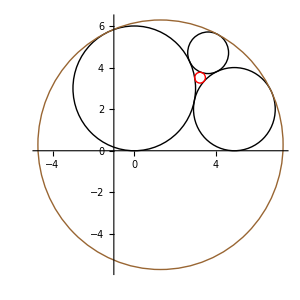

```mathematica
uDisplayFiveCircles[3,2,1]
```

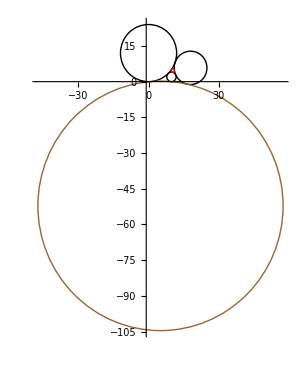

```mathematica
uDisplayFiveCircles[12, 2, 7]
```

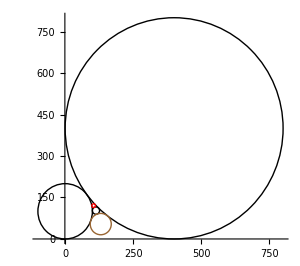

```mathematica
uDisplayFiveCircles[100,400,13.2]
```

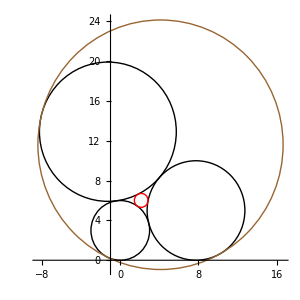

```mathematica
uDisplayFiveCircles[3,5,7]
```